# Introduction to Wolfram Language

## Functions

All function use square brackets, and have names that starts with capital letters.

```mathematica
Times[2,Plus[3,4]]
```

14

```mathematica
Times[5,4,3,2]
```

120

```mathematica
Times[Plus[8,7], Plus[9,2]]
```

165

```mathematica
Apply[Times,Apply[Plus, {{8,7},{9,2}},2]]
```

165

```mathematica
Times@@Plus@@@{{8,7},{9,2}}
```

165

## Lists

```mathematica
ListPlot[Join[Range[20],Reverse[Range[20]],RandomInteger[20,20]],Filling->10,PlotTheme -> {"OpenMarkersThick", "LargeLabels"},FillingStyle->{Blue,Red},GridLines->{None,{{10,{Black,Thick}}}}]
```

-Graphics-

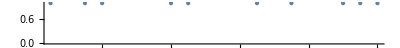

```mathematica
NumberLinePlot[RandomSample[Range[20],10]]
```

```mathematica
PieChart[Range[10],SectorOrigin->{Automatic,1},PerformanceGoal->"Quality"]
```

-Graphics-

```mathematica
Take[Range[10],5]
```

{1,2,3,4,5}

```mathematica
Drop[Range[10],5]
```

{6,7,8,9,10}

```mathematica
Rest[Range[10]]
```

{2,3,4,5,6,7,8,9,10}

```mathematica
Most[Range[10]]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
(* use table to make list*)
Table[{1,2},5]
```

{{1,2},{1,2},{1,2},{1,2},{1,2}}

```mathematica
Table[n-1,{n,1,10}]
```

{0,1,2,3,4,5,6,7,8,9}

```mathematica
Table[Range[n],{n,1,10}] //MatrixForm
```

({1}
{1,2}
{1,2,3}
{1,2,3,4}
{1,2,3,4,5}
{1,2,3,4,5,6}
{1,2,3,4,5,6,7}
{1,2,3,4,5,6,7,8}
{1,2,3,4,5,6,7,8,9}
{1,2,3,4,5,6,7,8,9,10})

```mathematica
Table[Range[n],{n,1,10}] // Column
```

{1}
{1,2}
{1,2,3}
{1,2,3,4}
{1,2,3,4,5}
{1,2,3,4,5,6}
{1,2,3,4,5,6,7}
{1,2,3,4,5,6,7,8}
{1,2,3,4,5,6,7,8,9}
{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[Column[Range[n]],{n,1,10}]
```

{1,1
2,1
2
3,1
2
3
4,1
2
3
4
5,1
2
3
4
5
6,1
2
3
4
5
6
7,1
2
3
4
5
6
7
8,1
2
3
4
5
6
7
8
9,1
2
3
4
5
6
7
8
9
10}

## Colors and Graphics

```mathematica
Table[RGBColor[0.5,g,0.5],{g,0,1,0.05}]
```

{RGBColor[0.5, 0., 0.5],RGBColor[0.5, 0.05, 0.5],RGBColor[0.5, 0.1, 0.5],RGBColor[0.5, 0.15000000000000002, 0.5],RGBColor[0.5, 0.2, 0.5],RGBColor[0.5, 0.25, 0.5],RGBColor[0.5, 0.30000000000000004, 0.5],RGBColor[0.5, 0.35000000000000003, 0.5],RGBColor[0.5, 0.4, 0.5],RGBColor[0.5, 0.45, 0.5],RGBColor[0.5, 0.5, 0.5],RGBColor[0.5, 0.55, 0.5],RGBColor[0.5, 0.6000000000000001, 0.5],RGBColor[0.5, 0.65, 0.5],RGBColor[0.5, 0.7000000000000001, 0.5],RGBColor[0.5, 0.75, 0.5],RGBColor[0.5, 0.8, 0.5],RGBColor[0.5, 0.8500000000000001, 0.5],RGBColor[0.5, 0.9, 0.5],RGBColor[0.5, 0.9500000000000001, 0.5],RGBColor[0.5, 1., 0.5]}

```mathematica
Table[Hue[x],{x,0,1,0.05}]
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

```mathematica
Table[Style[RandomInteger[10],RandomColor[],RandomInteger[{10,30}]],{20}]
```

{6,10,0,2,1,8,10,6,4,10,1,1,3,7,0,6,10,3,8,10}

```mathematica
ColorData["Named"]
```

{Atoms,Crayola,GeologicAges,HTML,Legacy,WebSafe}

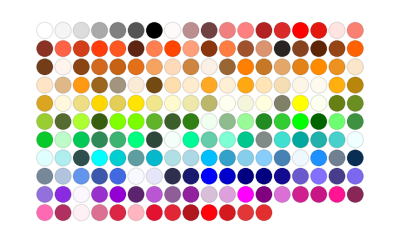

```mathematica
ColorData["Legacy","Image"]
```

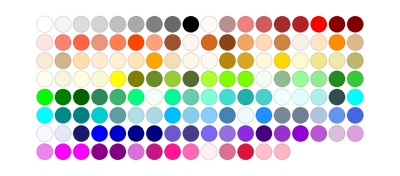

```mathematica
ColorData["HTML","Image"]
```

```mathematica
ColorData["GeologicAges","ColorRules"]
```

{Phanerozoic→RGBColor[0.690196, 0.886275, 0.819608],Cenozoic→RGBColor[1., 1., 0.],Quaternary→RGBColor[1., 1., 0.301961],Holocene→RGBColor[1., 1., 0.701961],Pleistocene→RGBColor[1., 0.921569, 0.384314],Neogene→RGBColor[0.992157, 0.8, 0.541176],Pliocene→RGBColor[0.996078, 0.921569, 0.67451],Miocene→RGBColor[1., 0.870588, 0.],Paleogene→RGBColor[1., 0.701961, 0.],Oligocene→RGBColor[0.917647, 0.776471, 0.447059],Eocene→RGBColor[0.917647, 0.678431, 0.262745],Paleocene→RGBColor[0.921569, 0.576471, 0.00392157],Mesozoic→RGBColor[0.498039, 0.678431, 0.317647],Cretaceous→RGBColor[0.498039, 0.764706, 0.109804],UpperCretaceous→RGBColor[0.870588, 0.945098, 0.592157],LowerCretaceous→RGBColor[0.701961, 0.87451, 0.498039],Jurassic→RGBColor[0.301961, 0.705882, 0.494118],UpperJurassic→RGBColor[0.8, 0.921569, 0.772549],MiddleJurassic→RGBColor[0.498039, 0.792157, 0.576471],LowerJurassic→RGBColor[0.4, 0.752941, 0.572549],Triassic→RGBColor[0.403922, 0.764706, 0.717647],UpperTriassic→RGBColor[0.8, 0.92549, 0.882353],MiddleTriassic→RGBColor[0.6, 0.843137, 0.745098],LowerTriassic→RGBColor[0.403922, 0.701961, 0.623529],Paleozoic→RGBColor[0.501961, 0.709804, 0.835294],Permian→RGBColor[0.403922, 0.776471, 0.866667],Lopingian→RGBColor[0.701961, 0.890196, 0.933333],Guadalupian→RGBColor[0.6, 0.847059, 0.847059],Cisuralian→RGBColor[0.501961, 0.807843, 0.788235],Carboniferous→RGBColor[0.6, 0.741176, 0.854902],Pennsylvanian→RGBColor[0.407843, 0.623529, 0.792157],Mississippian→RGBColor[0.501961, 0.568627, 0.678431],Devonian→RGBColor[0.6, 0.6, 0.788235],UpperDevonian→RGBColor[0.796078, 0.741176, 0.862745],MiddleDevonian→RGBColor[0.6, 0.513725, 0.745098],LowerDevonian→RGBColor[0.501961, 0.490196, 0.729412],Silurian→RGBColor[0.694118, 0.447059, 0.713725],Pridoli→RGBColor[0.913725, 0.780392, 0.886275],Ludlow→RGBColor[0.792157, 0.654902, 0.819608],Wenlock→RGBColor[0.694118, 0.537255, 0.701961],Llandovery→RGBColor[0.596078, 0.345098, 0.658824],Ordovician→RGBColor[0.976471, 0.505882, 0.65098],UpperOrdovician→RGBColor[0.984314, 0.705882, 0.741176],MiddleOrdovician→RGBColor[0.980392, 0.603922, 0.694118],LowerOrdovician→RGBColor[0.901961, 0.490196, 0.643137],Cambrian→RGBColor[0.984314, 0.501961, 0.372549],UpperCambrian→RGBColor[0.992157, 0.803922, 0.721569],MiddleCambrian→RGBColor[0.909804, 0.682353, 0.592157],LowerCambrian→RGBColor[0.905882, 0.486275, 0.447059],Precambrian→RGBColor[0.698039, 0.52549, 0.32549],Proterozoic→RGBColor[0.8, 0.847059, 0.568627],Neoproterozoic→RGBColor[0.792157, 0.647059, 0.584314],Ediacaran→RGBColor[0.917647, 0.847059, 0.737255],Cryogenian→RGBColor[0.862745, 0.670588, 0.666667],Tonian→RGBColor[0.796078, 0.643137, 0.423529],Mesoproterozoic→RGBColor[0.866667, 0.760784, 0.533333],Stenian→RGBColor[0.866667, 0.760784, 0.533333],Ectasian→RGBColor[0.866667, 0.760784, 0.533333],Calymmian→RGBColor[0.866667, 0.760784, 0.533333],Paleoproterozoic→RGBColor[0.701961, 0.698039, 0.368627],Statherian→RGBColor[0.701961, 0.698039, 0.368627],Orosirian→RGBColor[0.701961, 0.698039, 0.368627],Rhyacian→RGBColor[0.701961, 0.698039, 0.368627],Siderian→RGBColor[0.701961, 0.698039, 0.368627],Archean→RGBColor[0.6, 0.678431, 0.67451],Neoarchean→RGBColor[0.796078, 0.803922, 0.784314],Mesoarchean→RGBColor[0.698039, 0.709804, 0.686275],Paleoarchean→RGBColor[0.6, 0.592157, 0.568627],Eoarchean→RGBColor[0.501961, 0.564706, 0.564706],Hadean→RGBColor[0.5, 0.5, 0.56]}

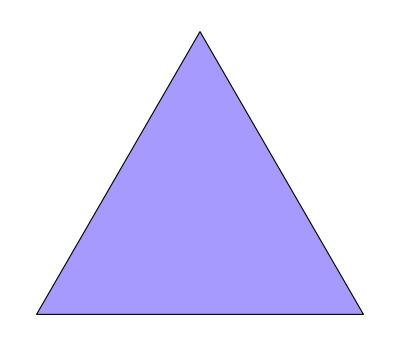
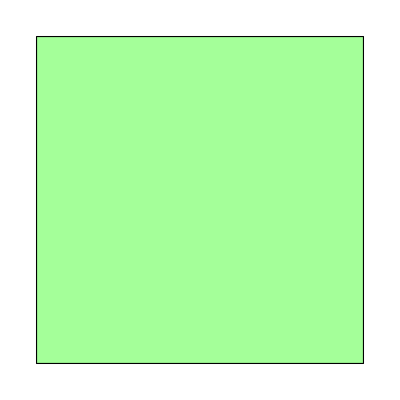
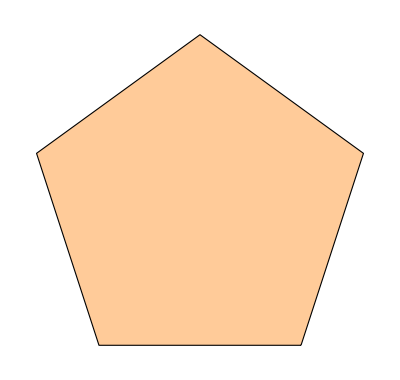
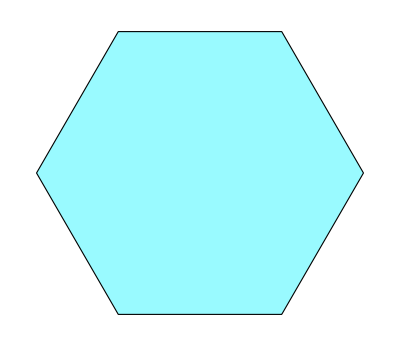
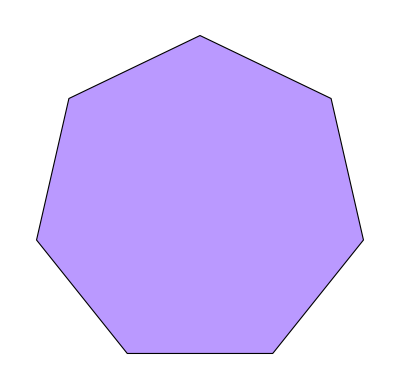
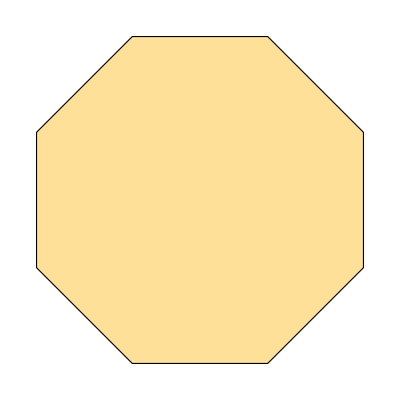
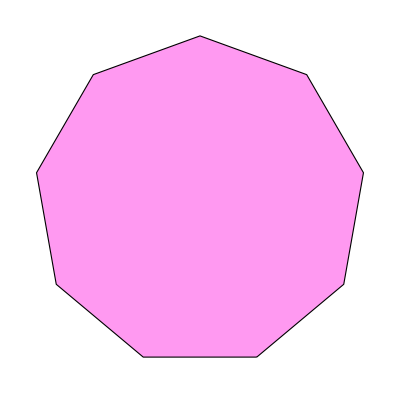
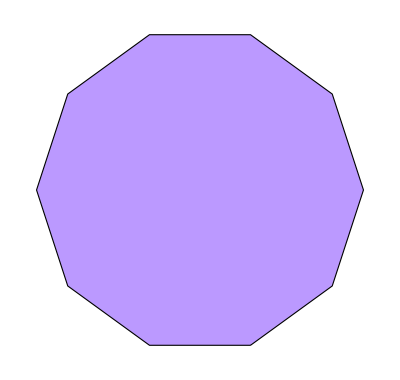

```mathematica
Graphics[{EdgeForm[Black],FaceForm[{Opacity[0.4],Hue[RandomReal[]]}],RegularPolygon[#]}]&/@Range[3,10]
```

## Manipulation

```mathematica
Manipulate[BarChart[RandomInteger[{5,20},a]],{a,5,10,1}]
```

```mathematica
Manipulate[Graphics[Table[{Hue[t/n],Thick, 
   Circle[{Cos[2 Pi t/n], Sin[2 Pi t/n]}, 1]}, {t, n}]],{{n,10},3,30,1}]
```

```mathematica
a=ExampleData[{"TestImage", "Mandrill"}]
```

-Graphics-

```mathematica
Manipulate[Binarize[a,t],{{t,0.5},0,1}]
```

## Strings and Text

```mathematica
Take[WordList[],100]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess,abbey,abbot,abbreviate,abbreviated,abbreviation,abdicate,abdication,abdomen,abdominal,abduct,abducting,abduction,abductor,abeam,abed,aberrant,aberration,abet,abettor,abeyance,abhor,abhorrence,abhorrent,abidance,abide,abiding,ability,abject,abjection,abjectly,abjuration,abjure,ablate,ablated,ablation,ablative,ablaze,able,abloom,ablution,ably,abnegate,abnegation,abnormal,abnormality,abnormally,aboard,abode,abolish,abolition,abolitionism,abolitionist,abominable,abominably,abominate,abomination,aboriginal,aborigine,abort,abortion,abortionist,abortive,abortively,abound,abounding,about,above,aboveboard,abracadabra,abrade,abrasion,abrasive,abrasiveness,abreast,abridge,abridged,abridgment,abroad,abrogate,abrogation}

```mathematica
wordsLengthCounts = Counts[StringLength[WordList[]]]
```

<|1→2,3→596,8→5770,5→3034,6→4622,7→5515,9→5416,11→3124,4→1914,10→4387,12→2094,14→661,16→159,13→1356,15→357,2→63,17→70,20→7,18→19,19→8,21→1,23→1|>

```mathematica
ListPlot[wordsLengthCounts,Filling->0,AxesLabel->{"Word Length","Counts"},Ticks->{Keys[wordsLengthCounts],Automatic}]
```

-Graphics-

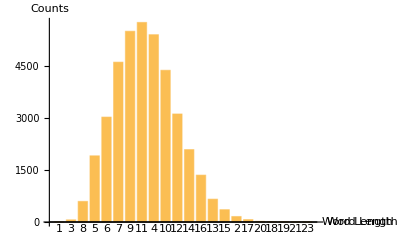

```mathematica
BarChart[KeySort[wordsLengthCounts],AxesLabel->{"Word Length","Counts"},ChartLabels->Keys[wordsLengthCounts]]
```

```mathematica
extrudeText[text_]:=Block[{img,res},
img=Rasterize[Style[text,100]];
res = ImageMesh[img];
RegionProduct[res,Line[{{0.},{10.}}]]
]
```

```mathematica
extrudeText["ABC"]
```

-Graphics3D-

## Arrays, lists of lists

```mathematica
Table[i*j, {i,5},{j,6}] //Grid
```

1 | 2 | 3 | 4 | 5 | 6
2 | 4 | 6 | 8 | 10 | 12
3 | 6 | 9 | 12 | 15 | 18
4 | 8 | 12 | 16 | 20 | 24
5 | 10 | 15 | 20 | 25 | 30

```mathematica
ArrayPlot[Table[i*j,{i,5},{j,6}]]
```

-Graphics-

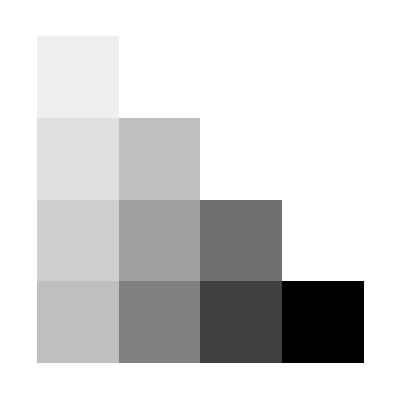

```mathematica
ArrayPlot[Table[i*j,{i,4},{j,i}] ]
```

```mathematica
Graphics[Table[Circle[{0,x},Abs@x],{x,-10,10,0.5}]~Join~Table[Circle[{x,0},Abs@x],{x,-10,10,1}]]
```

-Graphics-

```mathematica
Graphics3D[Table[Sphere[{x,y,z},0.5],{x,10},{y,x},{z,y}],Boxed->False]
```

-Graphics3D-

## Real-World Data

```mathematica
LinguisticAssistant
```

United States

```mathematica
InputForm[LinguisticAssistant]
```

"Entity[\"Country\", \"UnitedStates\"]"

```mathematica
CountryData["UnitedStates"]
```

United States

```mathematica
InputForm[CountryData["UnitedStates"]]
```

"Entity[\"Country\", \"UnitedStates\"]"

```mathematica
LinguisticAssistant
```

2.6 h

```mathematica
InputForm[LinguisticAssistant]
```

"Quantity[2.6, \"Hours\"]"

```mathematica
Quantity[2.6, "Hours"]
```

2.6 h

```mathematica
Quantity[7.5, "Feet"] + Quantity[14, "cm"]
```

242.6 cm

```mathematica
LinguisticAssistant+LinguisticAssistant
```

242.6 cm

```mathematica
N@UnitConvert[Quantity[100,"lb"],"kg"]
```

45.3592 kg

```mathematica
EarthquakeData[Entity["Earthquake","nc73666231"]]
```

Missing[NotAvailable]

{"type":"Feature","properties":{"mag":6.2,"place":"38km W of Petrolia, CA","time":1640031019100,"updated":1640430417695,"tz":null,"url":"https://earthquake.usgs.gov/earthquakes/eventpage/nc73666231","detail":"https://earthquake.usgs.gov/earthquakes/feed/v1.0/detail/nc73666231.geojson","felt":4372,"cdi":7,"mmi":6.936,"alert":"yellow","status":"reviewed","tsunami":1,"sig":1350,"net":"nc","code":"73666231","ids":",ew1640031020,nc73666231,at00r4fk16,us6000gdxq,","sources":",ew,nc,at,us,","types":",dyfi,focal-mechanism,general-text,ground-failure,impact-link,losspager,moment-tensor,nearby-cities,oaf,origin,phase-data,scitech-link,shake-alert,shakemap,","nst":118,"dmin":0.2951,"rms":0.22,"gap":224,"magType":"mw","type":"earthquake","title":"M 6.2 - 38km W of Petrolia, CA"},"geometry":{"type":"Point","coordinates":[-124.727,40.314,14.85]},"id":"nc73666231"}

```mathematica
data = EarthquakeData[GeoPosition[{40.31,-124.7 }],6]
```

<|centennial625301→<|Period→July 26, 1890 3:40 amGMT-6,AzimuthalGap→Missing[NotAvailable],Depth→Missing[NotAvailable],5,Position→GeoPosition[{40.5,-124.2}],PositionMethod→Missing[NotAvailable]|>,23,ncnc73666231→<|Period→1,8,1|>|>
 |  |  |  |

```mathematica
EarthquakeData[Entity["Earthquake","ncnc73666231"]]
```

<|Period→December 20, 2021 2:10 pmGMT-6,Magnitude→6.2,Position→GeoPosition[{40.314,-124.727}]|>

```mathematica
mintemp=(Normal@WeatherData["KBMG","MinTemperature",{{#,12,25},{#,12,25},"Day"}])&/@Range[1991,2021,1];
```

```mathematica
maxtemp=(Normal@WeatherData["KBMG","MaxTemperature",{{#,12,25},{#,12,25},"Day"}])&/@Range[1991,2021,1];
```

```mathematica
mintemp = DeleteMissing[Flatten[mintemp,1]]
```

{{December 25, 1991 12:00 amGMT-6,-6 °C},{December 25, 1992 12:00 amGMT-6,-7.28 °C},{December 25, 1993 12:00 amGMT-6,-10 °C},{December 25, 1994 12:00 amGMT-6,-1.72 °C},{December 25, 1995 12:00 amGMT-6,-5 °C},{December 25, 1996 12:00 amGMT-6,-11 °C},{December 25, 1998 12:00 amGMT-6,-12.78 °C},{December 25, 1999 12:00 amGMT-6,-16 °C},{December 25, 2000 12:00 amGMT-6,-23 °C},{December 25, 2001 12:00 amGMT-6,-9.39 °C},{December 25, 2002 12:00 amGMT-6,-4 °C},{December 25, 2003 12:00 amGMT-6,-6 °C},{December 25, 2004 12:00 amGMT-6,-28.28 °C},{December 25, 2005 12:00 amGMT-6,1 °C},{December 25, 2006 12:00 amGMT-6,1.72 °C},{December 25, 2007 12:00 amGMT-6,-6.72 °C},{December 25, 2008 12:00 amGMT-6,-9.39 °C},{December 25, 2009 12:00 amGMT-6,-1.11 °C},{December 25, 2011 12:00 amGMT-6,0.61 °C},{December 25, 2012 12:00 amGMT-6,-1.11 °C},{December 25, 2013 12:00 amGMT-6,-8.28 °C},{December 25, 2014 12:00 amGMT-6,2.22 °C},{December 25, 2015 12:00 amGMT-6,10 °C},{December 25, 2016 12:00 amGMT-6,2.22 °C},{December 25, 2017 12:00 amGMT-6,-7 °C},{December 25, 2018 12:00 amGMT-6,0 °C},{December 25, 2019 12:00 amGMT-6,-1.11 °C},{December 25, 2020 12:00 amGMT-6,-12.22 °C},{December 25, 2021 12:00 amGMT-6,16.72 °C}}

```mathematica
maxtemp = DeleteMissing[Flatten[maxtemp,1]]
```

{{December 25, 1991 12:00 amGMT-6,10 °C},{December 25, 1992 12:00 amGMT-6,1.61 °C},{December 25, 1993 12:00 amGMT-6,-2.78 °C},{December 25, 1994 12:00 amGMT-6,8.78 °C},{December 25, 1995 12:00 amGMT-6,-4.5 °C},{December 25, 1996 12:00 amGMT-6,-3 °C},{December 25, 1998 12:00 amGMT-6,-0.61 °C},{December 25, 1999 12:00 amGMT-6,-3 °C},{December 25, 2000 12:00 amGMT-6,-7 °C},{December 25, 2001 12:00 amGMT-6,-1.72 °C},{December 25, 2002 12:00 amGMT-6,-2 °C},{December 25, 2003 12:00 amGMT-6,2 °C},{December 25, 2004 12:00 amGMT-6,-5.61 °C},{December 25, 2005 12:00 amGMT-6,7 °C},{December 25, 2006 12:00 amGMT-6,5 °C},{December 25, 2007 12:00 amGMT-6,8.89 °C},{December 25, 2008 12:00 amGMT-6,1.11 °C},{December 25, 2009 12:00 amGMT-6,9.39 °C},{December 25, 2011 12:00 amGMT-6,1.72 °C},{December 25, 2012 12:00 amGMT-6,1.11 °C},{December 25, 2013 12:00 amGMT-6,-6.72 °C},{December 25, 2014 12:00 amGMT-6,3.28 °C},{December 25, 2015 12:00 amGMT-6,12.22 °C},{December 25, 2016 12:00 amGMT-6,5.61 °C},{December 25, 2017 12:00 amGMT-6,-5.61 °C},{December 25, 2018 12:00 amGMT-6,8.28 °C},{December 25, 2019 12:00 amGMT-6,18.89 °C},{December 25, 2020 12:00 amGMT-6,-7.22 °C},{December 25, 2021 12:00 amGMT-6,17.78 °C}}

```mathematica
DateListPlot[{maxtemp,mintemp},PlotTheme->"Scientific",Filling->{1 -> {2}},PlotLabel->"Min/Max Temperature on Christmas Day 1991-2021",Mesh->Full,PlotMarkers->Automatic,PlotLegends->{"Max","Min"},FrameLabel->{"Year","Temperature°"},LabelStyle->{Bold,FontSize->12},ImageSize->800,PerformanceGoal->"Quality"]
```

-Graphics-

## Dates and Times

```mathematica
Now
```

December 27, 2021 6:40 pmGMT-6

```mathematica
Now - LinguisticAssistant
```

December 26, 2021 6:41 pmGMT-6

```mathematica
Now - Quantity[1,"Day"]
```

December 26, 2021 6:41 pmGMT-6

```mathematica
Now - DateObject[{1988, 6, 23}]
```

12240. days

```mathematica
DayCount[{2021,1,1},{2021,12,27}] (* Day number shall be daycount + 1 *)
```

360

```mathematica
DateObject[{2021,1,1}] + Quantity[360, "Day"]
```

Mon 27 Dec 2021

```mathematica
DateValue[{2021,12,27},"DayOfYear"]
```

361

## Options

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Automatic,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
SetOptions[ListPlot, LabelStyle->Large,Filling->Bottom]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→Bottom,FillingStyle→Bottom,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Large,LabelStyle→Large,MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

```mathematica
ListPlot[RandomReal[10,10]->Callouts]
```

-Graphics-

```mathematica
SetOptions[ListPlot,LabelStyle->Automatic,Filling->Automatic]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→Automatic,FillingStyle→Bottom,FormatType:>TraditionalForm,Frame→Automatic,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,InterpolationOrder→None,IntervalMarkers→Automatic,IntervalMarkersStyle→Automatic,Joined→False,LabelingFunction→Automatic,LabelingSize→Large,LabelStyle→Automatic,MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,MultiaxisArrangement→None,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLabels→None,PlotLayout→Overlaid,PlotLegends→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,ScalingFunctions→None,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{}}

## Graphs and Networks

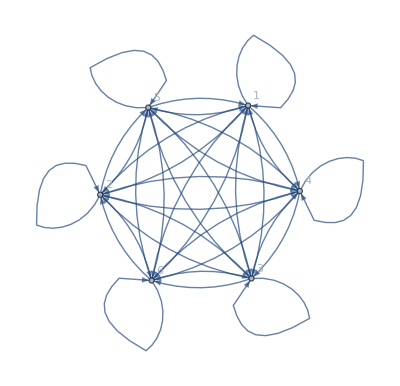

```mathematica
Graph[Flatten@Table[i->j,{i,6},{j,6}],VertexLabels->All]
```

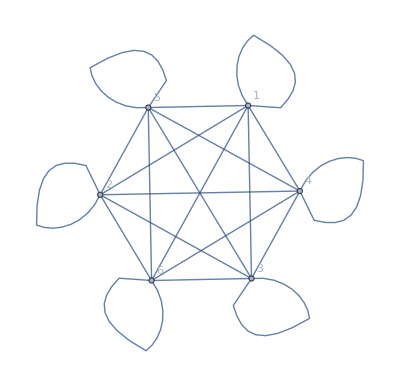

```mathematica
UndirectedGraph[Flatten@Table[i->j,{i,6},{j,6}],VertexLabels->All]
```

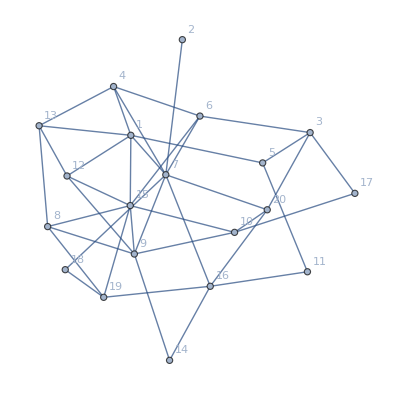

```mathematica
aG =RandomGraph[{20,40},VertexLabels->All]
```

```mathematica
apath = FindShortestPath[aG,13,11]
```

{13,1,5,11}

```mathematica
HighlightGraph[aG,PathGraph[apath]]
```

-Graphics-

## Ways to Apply Functions

```mathematica
f@x
```

f[x]

```mathematica
f@g@h@x
```

f[g[h[x]]]

```mathematica
(* afterthought *)
x //f
```

f[x]

```mathematica
x//h//g//f
```

f[g[h[x]]]

```mathematica
(f@g@h@x) === (x//h//g//f)
```

True

```mathematica
(* /@ apply to each element, map f over list *)
```

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
f@{1,2,3}
```

f[{1,2,3}]

```mathematica
f@@{1,2,3}
```

f[1,2,3]

```mathematica
Framed@{x,y,z}
```

{x,y,z}

```mathematica
Framed/@{x,y,x}
```

{x,y,x}

```mathematica
(* listable function *)
N[{1/2,1/3,1/4}]
```

{0.5,0.333333,0.25}

```mathematica
Range[{2,3,4}]
```

{{1,2},{1,2,3},{1,2,3,4}}

```mathematica
(* pure function *)
Rotate[Framed@"Hello",#]&/@{30 Degree, 90 Degree,180 Degree,270 Degree}
```

{Hello,Hello,Hello,Hello}

```mathematica
Framed[Column[{#, ColorNegate[#]}]] & /@ {Red, Green, Blue, Purple, 
  Orange}
```

{RGBColor[1, 0, 0]
RGBColor[0., 1., 1.],RGBColor[0, 1, 0]
RGBColor[1., 0., 1.],RGBColor[0, 0, 1]
RGBColor[1., 1., 0.],RGBColor[0.5, 0, 0.5]
RGBColor[0.5, 1., 0.5],RGBColor[1, 0.5, 0]
RGBColor[0., 0.5, 1.]}

```mathematica
(* Options can often be pure functions. It’s important to put parentheses around the whole pure function, as in ColorFunction->(Hue[#/4]&),*)
```

```mathematica
(* gives a list of the results of applying f to expr 0 through n times. *)
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

```mathematica
Nest[Framed,x,5]
```

x

```mathematica
NestList[2*#&,1,15]
```

{1,2,4,8,16,32,64,128,256,512,1024,2048,4096,8192,16384,32768}

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

```mathematica
NestList[Subsuperscript[#, #, #] &, x, 4]
```

{x,x_x^x,(x_x^x)_(x_x^x)^(x_x^x),((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)),(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))_(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))^(((x_x^x)_(x_x^x)^(x_x^x))_((x_x^x)_(x_x^x)^(x_x^x))^((x_x^x)_(x_x^x)^(x_x^x)))}

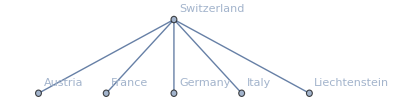

```mathematica
NestGraph[#["BorderingCountries"] &, 
 Entity["Country", "Switzerland"], 1, VertexLabels -> All,DirectedEdges->False]
```

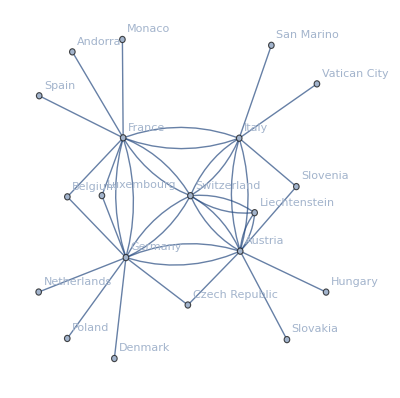

```mathematica
g2=NestGraph[#["BorderingCountries"] &, 
 Entity["Country", "Switzerland"], 2, VertexLabels -> All,DirectedEdges->False]
```

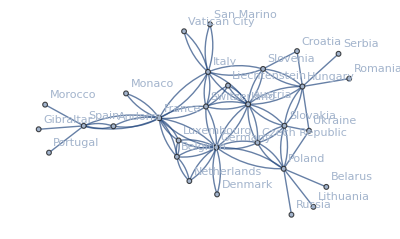

```mathematica
NestGraph[#["BorderingCountries"] &, 
 Entity["Country", "Switzerland"], 3, VertexLabels -> All,DirectedEdges->False]
```

```mathematica
Array[f,10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
f/@Range[10]
```

{f[1],f[2],f[3],f[4],f[5],f[6],f[7],f[8],f[9],f[10]}

```mathematica
Array[f,{3,4}] // Grid
```

f[1,1] | f[1,2] | f[1,3] | f[1,4]
f[2,1] | f[2,2] | f[2,3] | f[2,4]
f[3,1] | f[3,2] | f[3,3] | f[3,4]

```mathematica
Array[Times,{3,4}] //Grid
```

1 | 2 | 3 | 4
2 | 4 | 6 | 8
3 | 6 | 9 | 12

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

```mathematica
FoldList[f,x,{1,2,3,4,5}]
```

{x,f[x,1],f[f[x,1],2],f[f[f[x,1],2],3],f[f[f[f[x,1],2],3],4],f[f[f[f[f[x,1],2],3],4],5]}

```mathematica
Accumulate[{1,2,3,4,5}]
```

{1,3,6,10,15}

```mathematica
FoldList[Plus,{1,2,3,4,5}]
```

{1,3,6,10,15}

## More on Lists

```mathematica
alist = {{1,2},{3,4},{5,6},{7,8}}
```

{{1,2},{3,4},{5,6},{7,8}}

```mathematica
blist =Transpose[alist]
```

{{1,3,5,7},{2,4,6,8}}

```mathematica
MatrixForm/@{alist, blist}
```

{(1 | 2
3 | 4
5 | 6
7 | 8),(1 | 3 | 5 | 7
2 | 4 | 6 | 8)}

```mathematica
Thread[{1,3,5,7,9}->{2,4,6,8,10}]
```

{1→2,3→4,5→6,7→8,9→10}

```mathematica
Thread[{1,3,5,7,9}*{2,4,6,8,10}]
```

{2,12,30,56,90}

```mathematica
{1,3,5,7,9}*{2,4,6,8,10}
```

{2,12,30,56,90}

```mathematica
Partition[Range[10],3]
```

{{1,2,3},{4,5,6},{7,8,9}}

```mathematica
Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Partition[Range[10],2,1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10}}

```mathematica
Partition[Range[10],2,2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
Partition[Range[10],2,3]
```

{{1,2},{4,5},{7,8}}

```mathematica
NestList[{{#,0},{#,#}}&,{{1}},2]//MatrixForm
```

({{1}}
{{{{1}},0},{{{1}},{{1}}}}
{{{{{{1}},0},{{{1}},{{1}}}},0},{{{{{1}},0},{{{1}},{{1}}}},{{{{1}},0},{{{1}},{{1}}}}}})

```mathematica
NestList[ArrayFlatten@{{#,0},{#,#}}&,{{1}},2]//MatrixForm
```

({{1}}
{{1,0},{1,1}}
{{1,0,0,0},{1,1,0,0},{1,0,1,0},{1,1,1,1}})


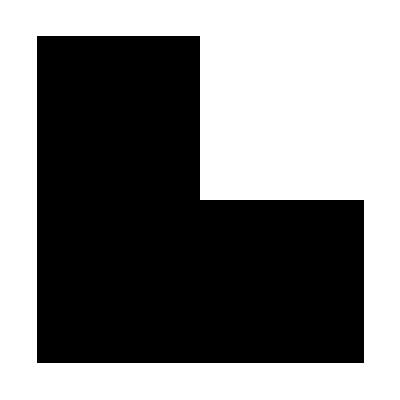
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot /@ NestList[ArrayFlatten@{{#,0},{#,#}}&,{{1}},5]
```

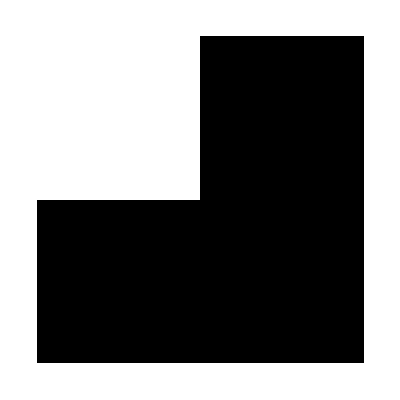
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot /@ NestList[ArrayFlatten@{{0,#},{#,#}}&,{{1}},5]
```

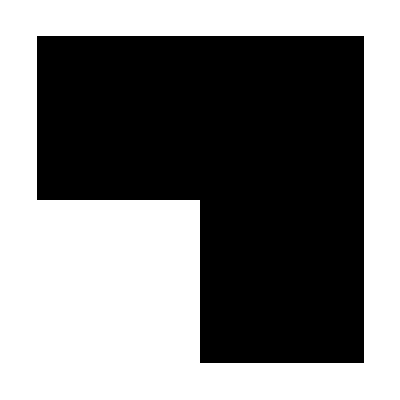
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot /@ NestList[ArrayFlatten@{{#,#},{0,#}}&,{{1}},5]
```

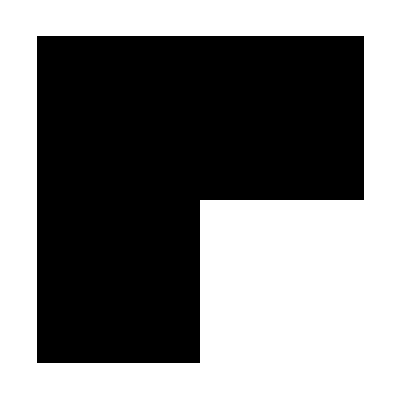
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot /@ NestList[ArrayFlatten@{{#,#},{#,0}}&,{{1}},5]
```

```mathematica
intList = RandomInteger[10,20]
```

{3,2,2,6,6,7,4,8,2,5,7,6,6,0,10,9,3,7,1,4}

```mathematica
Split[intList]
```

{{3},{2,2},{6,6},{7},{4},{8},{2},{5},{7},{6,6},{0},{10},{9},{3},{7},{1},{4}}

```mathematica
Split[intList,Less]
```

{{3},{2},{2,6},{6,7},{4,8},{2,5,7},{6},{6},{0,10},{9},{3,7},{1,4}}

```mathematica
Split[intList,Greater]
```

{{3,2},{2},{6},{6},{7,4},{8,2},{5},{7,6},{6,0},{10,9,3},{7,1},{4}}

```mathematica
Gather[Sort[intList]]
```

{{0},{1},{2,2,2},{3,3},{4,4},{5},{6,6,6,6},{7,7,7},{8},{9},{10}}

```mathematica
Gather[intList][[All,1]]
```

{3,2,6,7,4,8,5,0,10,9,1}

```mathematica
DeleteDuplicates[intList] (* DeleteDuplicates[list] does the same as Union[list], except it doesn’t reorder elements. *)
```

{3,2,6,7,4,8,5,0,10,9,1}

```mathematica
Union[intList]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Tally[intList]
```

{{3,2},{2,3},{6,4},{7,3},{4,2},{8,1},{5,1},{0,1},{10,1},{9,1},{1,1}}

```mathematica
Permutations[{x1,x2,x3}] //MatrixForm
```

(x1 | x2 | x3
x1 | x3 | x2
x2 | x1 | x3
x2 | x3 | x1
x3 | x1 | x2
x3 | x2 | x1)

```mathematica
Tuples[{x1,x2,x3},3]//MatrixForm
```

(x1 | x1 | x1
x1 | x1 | x2
x1 | x1 | x3
x1 | x2 | x1
x1 | x2 | x2
x1 | x2 | x3
x1 | x3 | x1
x1 | x3 | x2
x1 | x3 | x3
x2 | x1 | x1
x2 | x1 | x2
x2 | x1 | x3
x2 | x2 | x1
x2 | x2 | x2
x2 | x2 | x3
x2 | x3 | x1
x2 | x3 | x2
x2 | x3 | x3
x3 | x1 | x1
x3 | x1 | x2
x3 | x1 | x3
x3 | x2 | x1
x3 | x2 | x2
x3 | x2 | x3
x3 | x3 | x1
x3 | x3 | x2
x3 | x3 | x3)

```mathematica
Subsets[{x1,x2,x3}] //MatrixForm
```

({}
{x1}
{x2}
{x3}
{x1,x2}
{x1,x3}
{x2,x3}
{x1,x2,x3})

```mathematica
Graphics[Point@Tuples[Range[0,9],2],ImageSize->100]
```

-Graphics-

```mathematica
RandomChoice[intList,8]
```

{7,6,0,6,6,5,6,7}

```mathematica
RandomSample[intList,8]
```

{9,7,4,8,2,7,2,1}

```mathematica
intList[[{2,4}]] == Part[intList,{2,4}]
```

True

```mathematica
ReplacePart[intList,{3->x,5->y}]
```

{3,2,x,6,y,7,4,8,2,5,7,6,6,0,10,9,3,7,1,4}

```mathematica
Position[intList,3]
```

{{1},{17}}

```mathematica
ReplacePart[intList,Position[intList,3] ->y]
```

{y,2,2,6,6,7,4,8,2,5,7,6,6,0,10,9,y,7,1,4}

```mathematica
ReplaceAll[intList,{3->y}]
```

{y,2,2,6,6,7,4,8,2,5,7,6,6,0,10,9,y,7,1,4}

```mathematica
intList /. 3->y
```

{y,2,2,6,6,7,4,8,2,5,7,6,6,0,10,9,y,7,1,4}

```mathematica
TakeLargest[intList,5]
```

{10,9,8,7,7}

```mathematica
TakeSmallest[intList,5]
```

{0,1,2,2,2}

## Patterns

```mathematica
(* Patterns are a fundamental concept in the Wolfram Language. The pattern _ (read “blank”) stands for anything. *)
```

```mathematica
MatchQ[{a,b},{a,_}]
```

True

```mathematica
MatchQ[{a,b},{_,_}]
```

True

```mathematica
Cases[Partition[intList,2],{2,_}]
```

{{2,6},{2,5}}

```mathematica
(* The notation __ (“double blank”) in a pattern indicates any sequence of things.*)
```

```mathematica
intList /. 2->Red
```

{3,RGBColor[1, 0, 0],RGBColor[1, 0, 0],6,6,7,4,8,RGBColor[1, 0, 0],5,7,6,6,0,10,9,3,7,1,4}

```mathematica
intList /. {2->Red,6->Green}
```

{3,RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],7,4,8,RGBColor[1, 0, 0],5,7,RGBColor[0, 1, 0],RGBColor[0, 1, 0],0,10,9,3,7,1,4}

```mathematica
Cases[{{a, a, a}, {a, a}, {a, b}, {a, c}, {b, a}, {b, 
   b}, {c}, {a}, {b}}, {_, _}]
```

{{a,a},{a,b},{a,c},{b,a},{b,b}}

```mathematica
Cases[{{a, a, a}, {a, a}, {a, b}, {a, c}, {b, a}, {b, 
   b}, {c}, {a}, {b}}, {x_,x_}]  (* named pattern *)
```

{{a,a},{b,b}}

```mathematica
(* _ (Blank)— any expression (a "blank" to be filled in)
x_ — any expression, to be referred to as x
_h anything with head h
x_h anything with head h and call it x
__ (BlankSequence)— any sequence of one or more expression
___ (BlankNullSequence)— any sequence of zero or more expressions *)
```

```mathematica
digitback[n_Integer]:=Framed[Reverse[IntegerDigits[n]]]
```

```mathematica
digitback[2439]
```

{9,3,4,2}

```mathematica
digitback[3.1415]
```

digitback[3.1415]

```mathematica
pdigitback[n_Integer /; n > 0] := Framed[Reverse[IntegerDigits[n]],Background->LightGreen]
```

```mathematica
pdigitback[12346]
```

{6,4,3,2,1}

```mathematica
pdigitback[-12346]
```

pdigitback[-12346]

```mathematica
check[x_,y_]:=Red /; x>y
check[x_,y_]:=Green /; x≤y
```

```mathematica
{check[1,2],check[2,1]}
```

{RGBColor[0, 1, 0],RGBColor[1, 0, 0]}

```mathematica
(* sorting with pattern *)
alist = {5,4,1,3,2}
alist /. {x___,b_,a_,y___} /; b>a ->{x,a,b,y}
```

{5,4,1,3,2}

{4,5,1,3,2}

```mathematica
sortinglist = FixedPointList[(# /. {x___,b_,a_,y___}/; b>a ->{x,a,b,y})&,alist]
```

{{5,4,1,3,2},{4,5,1,3,2},{4,1,5,3,2},{1,4,5,3,2},{1,4,3,5,2},{1,3,4,5,2},{1,3,4,2,5},{1,3,2,4,5},{1,2,3,4,5},{1,2,3,4,5}}

```mathematica
ListLinePlot[Transpose@sortinglist]
```

-Graphics-

```mathematica
(* Transpose to find the list of elements appearing first, second, etc. at successive steps: *)
Transpose[sortinglist] //MatrixForm
```

(5 | 4 | 4 | 1 | 1 | 1 | 1 | 1 | 1 | 1
4 | 5 | 1 | 4 | 4 | 3 | 3 | 3 | 2 | 2
1 | 1 | 5 | 5 | 3 | 4 | 4 | 2 | 3 | 3
3 | 3 | 3 | 3 | 5 | 5 | 2 | 4 | 4 | 4
2 | 2 | 2 | 2 | 2 | 2 | 5 | 5 | 5 | 5)

```mathematica
(* string patter use ~~ *)
```

```mathematica
StringCases["the [important] word", "[" ~~ x__ ~~ "]" -> Framed[x]]
```

{important}

```mathematica
StringCases["now [several] important [words]", 
 "[" ~~ Shortest[x__] ~~ "]" -> Framed[x]]
```

{several,words}

```mathematica
StringReplace["now [several] important [words]", 
 "[" ~~ Shortest[x__] ~~ "]" :> ToUpperCase[x]]
```

now SEVERAL important WORDS

```mathematica
(* You can use | and .. in string patterns just like in ordinary patterns.*)
```

```mathematica
StringCases["12 and 123 and 4567 and 0x456", DigitCharacter ..]
```

{12,123,4567,0,456}

```mathematica
StringCases["12 and 123 and 4567 and 0x456", DigitCharacter ]
```

{1,2,1,2,3,4,5,6,7,0,4,5,6}

```mathematica
StringTemplate["`1` to the `2` is <*#1^#2*>"][2,50]
```

2 to the 50 is 1125899906842624

```mathematica
(* p.. is means Repeated[p] *)
{{}, {a, a}, {a, b}, {a, a, a}, {a}} /. {a ..} -> x
```

{{},x,{a,b},x,x}

```mathematica
{{}, {a, a}, {a, b}, {a, a, a}, {a}} /. a  -> x
```

{{},{x,x},{x,b},{x,x,x},{x}}

## Expression and Associations

```mathematica
(* length doesn't care about head *)
Length[f[x,y,z]]
```

3

```mathematica
Length[f[{x,y,z}]]
```

1

```mathematica
(* map also skip the head *)
Apply[f,g[x,y,z]]
```

f[x,y,z]

```mathematica
f /@ g[x,y,z]
```

g[f[x],f[y],f[z]]

```mathematica
Map[f,g[x,y,z]]
```

g[f[x],f[y],f[z]]

```mathematica
#1->#2 &@@{x,y}
```

x→y

```mathematica
Rule@@{x,y}
```

x→y

```mathematica
Rule@@@{{1,10},{2,20},{3,30}}
```

{1→10,2→20,3→30}

```mathematica
(* f@@list -> replace the head of list with f  Apply[f,expr]
   f@@@{list1,list2, ..} -> replace heeds of list1,list2, .. with f Apply[f,expr,{1}]*)
```

```mathematica
(* Associations are a kind of generalization of lists, in which every element has a key as well as a value. *)
Counts[{a, a, b, c, a, a, b, c, c, a, a}]
```

<|a→6,b→2,c→3|>

```mathematica
<|a -> 6, b -> 2, c -> 3|>[c]
```

3

```mathematica
f /@ <|a -> 6, b -> 2, c -> 3|>
```

<|a→f[6],b→f[2],c→f[3]|>

```mathematica
Sort[<|a -> 6, b -> 2, c -> 3|>]
```

<|b→2,c→3,a→6|>

```mathematica
KeySort[<|a -> 6, b -> 2, c -> 3|>]
```

<|a→6,b→2,c→3|>

```mathematica
Keys[<|a -> 6, b -> 2, c -> 3|>]
```

{a,b,c}

```mathematica
Values[<|a -> 6, b -> 2, c -> 3|>]
```

{6,2,3}

```mathematica
Normal[<|a -> 6, b -> 2, c -> 3|>]
```

{a→6,b→2,c→3}

```mathematica
Association[{a->6,b->2,c->3}]
```

<|a→6,b→2,c→3|>

## Layout and Display